# Reconocimiento de patrones: Tarea 4

### Carlos Manuel Rodríguez Martínez 17/05/2020

Definición de función objetivo

```mathematica
TargetFunction[x_]:=Sin[x];
```

Creación del conjunto de entrenamiento y de prueba.

```mathematica
{a,b}={-π,π};
δ = (b-a)/10;
baseFunction = Table[{x,TargetFunction[x]},{x,a,b,0.25*δ}];
trainingSet = Table[{x,TargetFunction[x]+RandomVariate[NormalDistribution[0,0.1]]},{x,a,b,δ}];
validationSet = Table[{x,TargetFunction[x]+RandomVariate[NormalDistribution[0,0.1]]},{x,Sort[RandomReal[{a,b},10]]}];
```

Gráfica del conjunto de entrenamiento y conjunto de prueba.

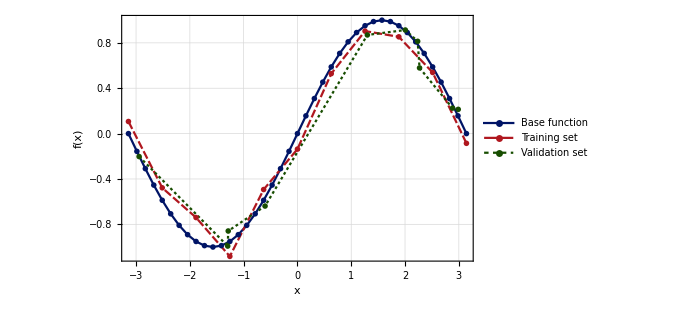

```mathematica
ListLinePlot[
{baseFunction,trainingSet,validationSet},
PlotLegends->{"Base function","Training set","Validation set"},
PlotTheme->"Monochrome",
FrameLabel->{Style["x",15], Style["f(x)",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
Joined->{True,True},
PlotStyle->{RGBColor[0., 0.08, 0.4],RGBColor[0.689993, 0.089999, 0.119999],RGBColor[0.09, 0.3, 0.]},
Frame->True,
ImageSize->500
]
```

Defininción de base y error

Aquí se definen las bases y una función auxiliar para expandir un vector de w sobre la base.

```mathematica
PolynomialBase[x_,n_]:=Table[If[i==0,1,x^i],{i,0,n-1}];
GaussianBase[x_,n_, σ_ : 1]:=Block[{δ = (b-a)/n},Table[Exp[- (x-(a+δ i))^2/(2 σ^2)],{i,0,n-1}]];
SigmoidBase[x_,n_, σ_ : 1]:=Block[{δ = (b-a)/n},Table[LogisticSigmoid[(x-(a+δ i))/σ],{i,0,n-1}]];

ExpandBase[x_,w_,baseFunction_]:=w.baseFunction[x,Length[w]];
```

Definición de matrices necesarias para el computo de la función de evidencia

```mathematica
PhiDesignMatrix[data_,n_,baseFunction_]:=Module[{base,x},
base = baseFunction[x,n];
Map[N[base/.{x->#}]&,data]
];
AHessianMatrix[Φ_,α_,β_]:=Block[{n,tr},
tr = Transpose[Φ].Φ;
n = Length[tr];
α IdentityMatrix[n]+β tr
];
MPosterior[Φ_,t_,α_,β_]:=Block[{A},
A = AHessianMatrix[Φ,α,β];
{β Inverse[A].Transpose[Φ].t}
];
Error[m_,Φ_,t_,α_,β_]:=β/2 Norm[First[Transpose[Transpose[{t}]-Φ.Transpose[m]]]]^2 + α/2 First[First[m.Transpose[m]]];
```

### Ejemplo con n = 5

```mathematica
Φ = PhiDesignMatrix[trainingSet[[All,1]],5,PolynomialBase];
```

```mathematica
MatrixForm[Φ]
```

(1. | -3.14159 | 9.8696 | -31.0063 | 97.4091
1. | -2.51327 | 6.31655 | -15.8752 | 39.8988
1. | -1.88496 | 3.55306 | -6.69736 | 12.6242
1. | -1.25664 | 1.57914 | -1.9844 | 2.49367
1. | -0.628319 | 0.394784 | -0.24805 | 0.155855
1. | 0. | 0. | 0. | 0.
1. | 0.628319 | 0.394784 | 0.24805 | 0.155855
1. | 1.25664 | 1.57914 | 1.9844 | 2.49367
1. | 1.88496 | 3.55306 | 6.69736 | 12.6242
1. | 2.51327 | 6.31655 | 15.8752 | 39.8988
1. | 3.14159 | 9.8696 | 31.0063 | 97.4091)

```mathematica
β = 1/0.1;
```

```mathematica
A = AHessianMatrix[Φ,5 10^-3,β];
```

```mathematica
MatrixForm[A]
```

(110.005 | 0. | 434.263 | 3.55271×10^-14 | 3051.63
0. | 434.268 | -3.55271×10^-14 | 3051.63 | -5.68434×10^-13
434.263 | -3.55271×10^-14 | 3051.64 | -5.68434×10^-13 | 25245.3
3.55271×10^-14 | 3051.63 | -5.68434×10^-13 | 25245.3 | 0.
3051.63 | -5.68434×10^-13 | 25245.3 | 0. | 224921.)

```mathematica
t = trainingSet[[All,2]];
m = MPosterior[Φ,t,5 10^-3,β]
```

{{-0.0688206,0.774661,0.0341111,-0.0837201,-0.00265165}}

```mathematica
Error[m,Φ,t,5 10^-3,β]
```

0.773951

Función de evidencia

```mathematica
EvidenceFunction[data_,α_,β_,M_,baseFunction_]:=Quiet@Block[{x,t,Φ,A,m,Np},
Np = Length[x];
x = data[[All,1]];
t = data[[All,2]];
Φ = PhiDesignMatrix[x,M,baseFunction];
A = AHessianMatrix[Φ,α,β];
m = MPosterior[Φ,t,α,β];

M/2 Log[α]+Np/2 Log[β]-Error[m,Φ,t,α,β]-1/2 Log[Det[A]]-Np/2 Log[2π]
];
```

Ajuste de mínimos cuadrados con Pseudo-Inversa Moore Penrose

```mathematica
MoorePenrosePseudoInverse[m_]:=Quiet@Inverse[Transpose[m].m].Transpose[m];
FitWithMPPseudoInverse[data_,n_,baseFunction_]:=Block[{ϕ},
ϕ = PhiDesignMatrix[data[[All,1]],n,baseFunction];
MoorePenrosePseudoInverse[ϕ].data[[All,2]]
];
FitMPExpressionWithBase[data_,x_,n_,baseFunction_]:=ExpandBase[x,FitWithMPPseudoInverse[data,n,baseFunction],baseFunction];
```

#### Base polinomial

{{1,-32.761},{2,-27.1898},{3,-33.4381},{4,-24.868},{5,-32.1219},{6,-38.9182},{7,-46.9133},{8,-55.2098},{9,-63.7111},{10,-72.2143}}

Valor óptimo: M = 4

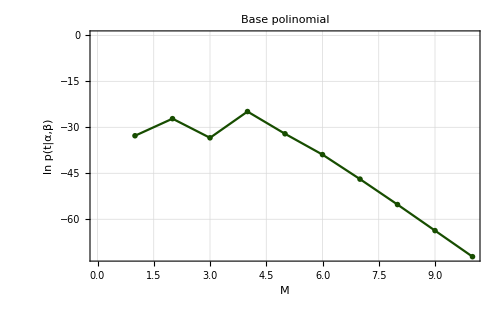

```mathematica
ev = Table[{M,EvidenceFunction[trainingSet,5 10^-3,β,M,PolynomialBase]},{M,1,10}]
Row[{"Valor óptimo: M = ",MaximalBy[ev,Last][[1,1]]}]
ListLinePlot[ev,
PlotTheme->"Monochrome",
FrameLabel->{Style["M",15], Style["ln p(t|α,β)",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
Joined->{True,True},
PlotStyle->{RGBColor[0., 0.08, 0.4],RGBColor[0.689993, 0.089999, 0.119999],RGBColor[0.09, 0.3, 0.]},
Frame->True,
ImageSize->500,
PlotLabel->"Base polinomial"
]
```

El mejor ajuste polinomial es:

```mathematica
bestPolynomial = FitMPExpressionWithBase[trainingSet,x,4,PolynomialBase]
```

0.0105989+0.859079 x+0.000464503 x^2-0.089849 x^3

#### Base sigmoide

{{1,-32.3894},{2,-18.9726},{3,-21.9066},{4,-14.3314},{5,-14.6613},{6,-15.0033},{7,-15.3063},{8,-15.5753},{9,-15.8171},{10,-16.0369}}

Valor óptimo: M = 4

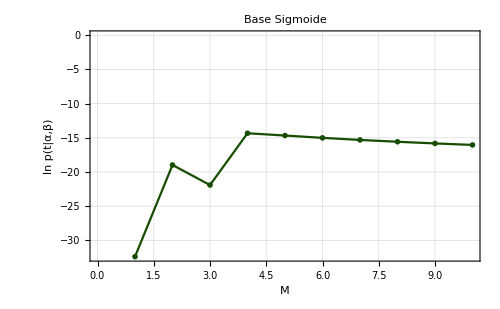

```mathematica
ev = Table[{M,EvidenceFunction[trainingSet,5 10^-3,β,M,SigmoidBase]},{M,1,10}]
Row[{"Valor óptimo: M = ",MaximalBy[ev,Last][[1,1]]}]
ListLinePlot[ev,
PlotTheme->"Monochrome",
FrameLabel->{Style["M",15], Style["ln p(t|α,β)",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
Joined->{True,True},
PlotStyle->{RGBColor[0., 0.08, 0.4],RGBColor[0.689993, 0.089999, 0.119999],RGBColor[0.09, 0.3, 0.]},
Frame->True,
ImageSize->500,
PlotLabel->"Base Sigmoide"
]
```

```mathematica
bestSigmoid = FitMPExpressionWithBase[trainingSet,x,4,SigmoidBase]
```

15.1108 LogisticSigmoid[x]-8.14292 LogisticSigmoid[-π/2+x]-9.69659 LogisticSigmoid[π/2+x]+1.93735 LogisticSigmoid[π+x]

#### Base gaussiana

{{1,-28.8934},{2,-33.1594},{3,-13.8412},{4,-17.1429},{5,-20.327},{6,-22.2169},{7,-23.5116},{8,-24.3223},{9,-24.9458},{10,-25.4628}}

Valor óptimo: M = 3

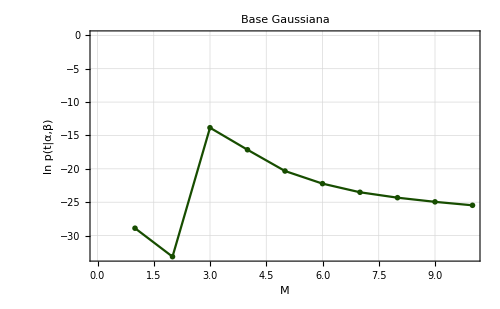

```mathematica
ev = Table[{M,EvidenceFunction[trainingSet,5 10^-3,β,M,GaussianBase]},{M,1,10}]
Row[{"Valor óptimo: M = ",MaximalBy[ev,Last][[1,1]]}]
ListLinePlot[ev,
PlotTheme->"Monochrome",
FrameLabel->{Style["M",15], Style["ln p(t|α,β)",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
Joined->{True,True},
PlotStyle->{RGBColor[0., 0.08, 0.4],RGBColor[0.689993, 0.089999, 0.119999],RGBColor[0.09, 0.3, 0.]},
Frame->True,
ImageSize->500,
PlotLabel->"Base Gaussiana"
]
```

```mathematica
bestGaussian= FitMPExpressionWithBase[trainingSet,x,3,GaussianBase]
```

1.20032 ⅇ^(-1/2 (-π/3+x)^2)-1.1673 ⅇ^(-1/2 (π/3+x)^2)-0.0203132 ⅇ^(-1/2 (π+x)^2)

#### Comparación

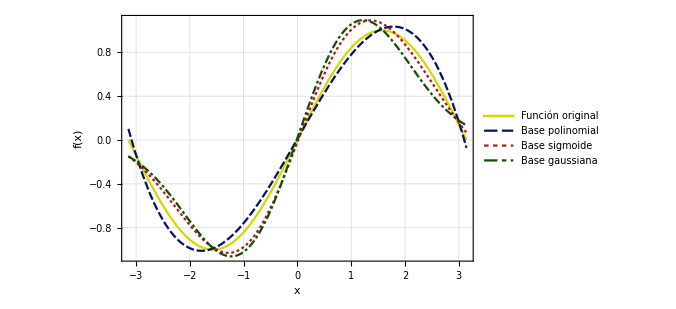

```mathematica
Plot[
{TargetFunction[x],bestPolynomial,bestSigmoid,bestGaussian},
{x,a,b},
PlotTheme->"Monochrome",
FrameLabel->{Style["x",15], Style["f(x)",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
PlotStyle->{RGBColor[0.84, 0.84, 0.],RGBColor[0., 0.08, 0.4],RGBColor[0.689993, 0.089999, 0.119999],RGBColor[0.09, 0.3, 0.]},
Frame->True,
ImageSize->500,
PlotLegends->{"Función original","Base polinomial", "Base sigmoide","Base gaussiana"}
]
```

Conclusión

```mathematica
evPol = Table[{M,EvidenceFunction[trainingSet,5 10^-3,β,M,PolynomialBase]},{M,1,10}];
evSig = Table[{M,EvidenceFunction[trainingSet,5 10^-3,β,M,SigmoidBase]},{M,1,10}];
evGauss = Table[{M,EvidenceFunction[trainingSet,5 10^-3,β,M,GaussianBase]},{M,1,10}];
```

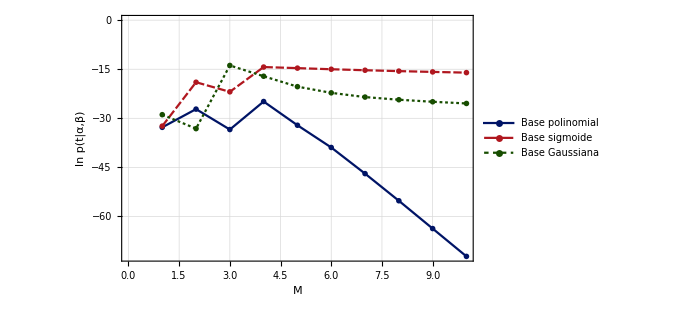

```mathematica
ListLinePlot[{evPol,evSig,evGauss},
PlotTheme->"Monochrome",
FrameLabel->{Style["M",15], Style["ln p(t|α,β)",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
Joined->{True,True},
PlotStyle->{RGBColor[0., 0.08, 0.4],RGBColor[0.689993, 0.089999, 0.119999],RGBColor[0.09, 0.3, 0.]},
Frame->True,
ImageSize->500,
PlotLegends->{"Base polinomial","Base sigmoide","Base Gaussiana"}
]
```

Observando los valores de la función de evidencia se puede concluir que la función de evidencia adquiere un valor máximo para la base Gaussiana con M = 3, por lo que se considera que proporciona el mejor ajuste de los datos.